```mathematica
Quit[]
```

## Residue method

### 1/16 unrefined index

```mathematica
Clear["Global`*"];

(* product of chracters *)
characterProduct[NN_,a_]:=characterProduct[NN,a]=Product[(Sum[w[i]^n/w[j]^n,{i,1,NN},{j,1,NN}]-1)^a[[n]],{n,1,Length[a]}]

(* generate a vector "a" with Sum[i a[[i]],{i,1,NN}] fixed to be L *)
power[NN_,a_]:=power[NN,a]=2 NN-2+2 Sum[i a[[i]],{i,1,Length[a]}]
aVectors[L_]:=aVectors[L]=Module[{partition,vector},
partition=IntegerPartitions[L];
vector[n_]:=Sum[Table[KroneckerDelta[n[[j]],i],{i,1,L}],{j,1,Length[n]}];
Table[vector[partition[[i]]],{i,1,Length[partition]}]
]


coefficient[a_]:=coefficient[a]=Product[1/a[[i]]!/(i^(a[[i]])),{i,1,Length[a]}]

f[x_]:=1-(1-x^2)^3/(1-x^3)^2

groupIntegrand[NN_,a_]:=groupIntegrand[NN,a]=characterProduct[NN,a](*Product[1/w[i],{i,1,NN-1}]*)(-1)^(NN(NN-1)/2)(*/Product[w[i]^(NN-1),{i,1,NN}]*)Product[(w[i]-w[j])^2,{i,1,NN},{j,1,i-1}]/.w[NN]->1/Product[w[i],{i,1,NN-1}]

Clear[groupIntegrandNumerator,groupIntegral,index]
groupIntegrandNumerator[NN_,a_]:=groupIntegrandNumerator[NN,a]=Numerator[groupIntegrand[NN,a]//Together]

groupIntegral[NN_,a_]:=groupIntegral[NN,a]=1/NN!Coefficient[ groupIntegrandNumerator[NN,a]//Expand,Product[w[i],{i,1,NN-1}]^power[NN,a] ]

index[NN_,L_]:=index[NN,L]=Module[{as},
as=aVectors[L];
Sum[Product[f[x^j]^as[[i,j]],{j,1,L}]groupIntegral[NN,as[[i]]]coefficient[as[[i]]],{i,1,Length[as]}]
]
```

```mathematica
NN=2;
LL=30;
AbsoluteTiming[Sum[index[NN,L],{L,0,LL/2}]+O[x]^(LL+1)]
```

{0.390262,1+6 x^4-6 x^5-7 x^6+18 x^7+6 x^8-36 x^9+6 x^10+84 x^11-80 x^12-132 x^13+309 x^14-18 x^15-567 x^16+516 x^17+613 x^18-1392 x^19-180 x^20+2884 x^21-1926 x^22-4242 x^23+7890 x^24+792 x^25-15876 x^26+13804 x^27+15177 x^28-37536 x^29+7049 x^30+O[x]^31}

```mathematica
NN=3;
LL=30;
AbsoluteTiming[Sum[index[NN,L],{L,0,LL/2}]+O[x]^(LL+1)]
```

{1.90819,1+6 x^4-6 x^5+3 x^6+6 x^7-16 x^9+27 x^10+18 x^11-87 x^12+96 x^13+54 x^14-222 x^15+132 x^16+210 x^17-235 x^18-468 x^19+1284 x^20-534 x^21-2268 x^22+4392 x^23-1995 x^24-4128 x^25+6957 x^26-1288 x^27-5310 x^28-2376 x^29+22695 x^30+O[x]^31}

```mathematica
NN=4;
LL=15;
AbsoluteTiming[Sum[index[NN,L],{L,0,LL/2}]+O[x]^(LL+1)]
```

{0.527629,1+6 x^4-6 x^5+3 x^6+6 x^7+15 x^8-36 x^9+24 x^10+36 x^11-37 x^12-30 x^13+78 x^14+88 x^15+O[x]^16}

### unflavored Schur index

```mathematica
Clear["Global`*"];

(* product of chracters *)
characterProduct[NN_,a_]:=characterProduct[NN,a]=Product[(Sum[w[i]^n/w[j]^n,{i,1,NN},{j,1,NN}]-1)^a[[n]],{n,1,Length[a]}]

(* generate a vector "a" with Sum[i a[[i]],{i,1,NN}] fixed to be L *)
power[NN_,a_]:=power[NN,a]=2 NN-2+2 Sum[i a[[i]],{i,1,Length[a]}]
aVectors[L_]:=aVectors[L]=Module[{partition,vector},
partition=IntegerPartitions[L];
vector[n_]:=Sum[Table[KroneckerDelta[n[[j]],i],{i,1,L}],{j,1,Length[n]}];
Table[vector[partition[[i]]],{i,1,Length[partition]}]
]


coefficient[a_]:=coefficient[a]=Product[1/a[[i]]!/(i^(a[[i]])),{i,1,Length[a]}]

f[x_]:=1-(1-x)^2/(1-x^2)

groupIntegrand[NN_,a_]:=groupIntegrand[NN,a]=characterProduct[NN,a](*Product[1/w[i],{i,1,NN-1}]*)(-1)^(NN(NN-1)/2)(*/Product[w[i]^(NN-1),{i,1,NN}]*)Product[(w[i]-w[j])^2,{i,1,NN},{j,1,i-1}]/.w[NN]->1/Product[w[i],{i,1,NN-1}]

Clear[groupIntegrandNumerator,groupIntegral,index]
groupIntegrandNumerator[NN_,a_]:=groupIntegrandNumerator[NN,a]=Numerator[groupIntegrand[NN,a]//Together]

groupIntegral[NN_,a_]:=groupIntegral[NN,a]=1/NN!Coefficient[ groupIntegrandNumerator[NN,a]//Expand,Product[w[i],{i,1,NN-1}]^power[NN,a] ]

index[NN_,L_]:=index[NN,L]=Module[{as},
as=aVectors[L];
Sum[Product[f[x^j]^as[[i,j]],{j,1,L}]groupIntegral[NN,as[[i]]]coefficient[as[[i]]],{i,1,Length[as]}]
]
```

```mathematica
NN=3;
LL=15;
AbsoluteTiming[Sum[index[NN,L],{L,0,LL}]+O[x]^(LL+1)]
```

{1.9267,1+3 x^2+4 x^4+7 x^6+6 x^8+12 x^10+8 x^12+15 x^14+O[x]^16}

### flavored Schur index

```mathematica
Clear["Global`*"];

(* product of chracters *)
characterProduct[NN_,a_]:=characterProduct[NN,a]=Product[(Sum[w[i]^n/w[j]^n,{i,1,NN},{j,1,NN}]-1)^a[[n]],{n,1,Length[a]}]

(* generate a vector "a" with Sum[i a[[i]],{i,1,NN}] fixed to be L *)
power[NN_,a_]:=power[NN,a]=2 NN-2+2 Sum[i a[[i]],{i,1,Length[a]}]
aVectors[L_]:=aVectors[L]=Module[{partition,vector},
partition=IntegerPartitions[L];
vector[n_]:=Sum[Table[KroneckerDelta[n[[j]],i],{i,1,L}],{j,1,Length[n]}];
Table[vector[partition[[i]]],{i,1,Length[partition]}]
]


coefficient[a_]:=coefficient[a]=Product[1/a[[i]]!/(i^(a[[i]])),{i,1,Length[a]}]

f[x_,b_]:=1-((1-b x)(1-b^-1 x))/(1-x^2)

groupIntegrand[NN_,a_]:=groupIntegrand[NN,a]=characterProduct[NN,a](*Product[1/w[i],{i,1,NN-1}]*)(-1)^(NN(NN-1)/2)(*/Product[w[i]^(NN-1),{i,1,NN}]*)Product[(w[i]-w[j])^2,{i,1,NN},{j,1,i-1}]/.w[NN]->1/Product[w[i],{i,1,NN-1}]

Clear[groupIntegrandNumerator,groupIntegral,index]
groupIntegrandNumerator[NN_,a_]:=groupIntegrandNumerator[NN,a]=Numerator[groupIntegrand[NN,a]//Together]

groupIntegral[NN_,a_]:=groupIntegral[NN,a]=1/NN!Coefficient[ groupIntegrandNumerator[NN,a]//Expand,Product[w[i],{i,1,NN-1}]^power[NN,a] ]

index[NN_,L_]:=index[NN,L]=Module[{as},
as=aVectors[L];
Sum[Product[f[x^j,b^j]^as[[i,j]],{j,1,L}]groupIntegral[NN,as[[i]]]coefficient[as[[i]]],{i,1,Length[as]}]
]
```

```mathematica
NN=3;
LL=15;
AbsoluteTiming[tmp=Sum[index[NN,L],{L,0,LL}]+O[x]^(LL+1)//Simplify]
```

{2.46799,1+(1+1/b^2+b^2) x^2+((-1+b^2)^2 (1+b^2) x^3)/b^3+(2+1/b^4+b^4) x^4+((-1+b^2)^2 (1+b^2)^3 x^5)/b^5+(5+2/b^6-1/b^4-b^4+2 b^6) x^6+(1/b^7+3/b^3-4/b-4 b+3 b^3+b^7) x^7+(8+2/b^8+1/b^6-3/b^4-1/b^2-b^2-3 b^4+b^6+2 b^8) x^8+((-1+b^2)^2 (1+b^2)^3 (2-3 b^2+7 b^4-3 b^6+2 b^8) x^9)/b^9+(16+2/b^10+3/b^6-6/b^4-1/b^2-b^2-6 b^4+3 b^6+2 b^10) x^10+(2/b^11+1/b^9-3/b^7+13/b^3-13/b-13 b+13 b^3-3 b^7+b^9+2 b^11) x^11+(28+3/b^12-1/b^10+7/b^6-13/b^4-6/b^2-6 b^2-13 b^4+7 b^6-b^10+3 b^12) x^12+((-1+b^2)^2 (1+b^2)^3 (2-2 b^2+9 b^4-16 b^6+27 b^8-16 b^10+9 b^12-2 b^14+2 b^16) x^13)/b^13+(51+3/b^14+1/b^12-3/b^10+15/b^6-23/b^4-11/b^2-11 b^2-23 b^4+15 b^6-3 b^10+b^12+3 b^14) x^14+(3/b^15-1/b^13+7/b^9-15/b^7-2/b^5+47/b^3-39/b-39 b+47 b^3-2 b^5-15 b^7+7 b^9-b^13+3 b^15) x^15+O[x]^16}

#### With Simplify

```mathematica
NN=3;
Monitor[times=Table[AbsoluteTiming[tmp=Sum[index[NN,L],{L,0,LL}]+O[x]^(LL+1)//Simplify][[1]],{LL,0,25}];
,LL]
```

$Aborted

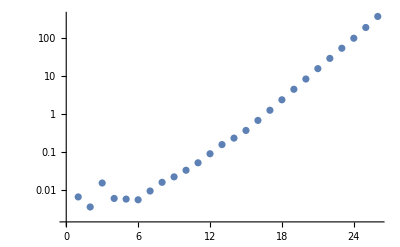

```mathematica
ListLogPlot[times]
```

```mathematica
(*ISU3L25=tmp;
Save[NotebookDirectory[]<>"index.m",{ISU3L25,index}];*)
```

```mathematica
(*Load[NotebookDirectory[]<>"index.m"];
tmp=ISU3L25;*)
```

#### Without Simplify

```mathematica
NN=3;
LL=30;
Timing[tmp=Sum[index[NN,L],{L,0,LL}]][[1]]
```

396.912

#### Analysis

```mathematica
tmp/.ξ->1
```

1+3 t^2+4 t^4+7 t^6+6 t^8+12 t^10+8 t^12+15 t^14+13 t^16+18 t^18+12 t^20+28 t^22+14 t^24+O[t]^26

```mathematica
tmp/.ξ->ⅈ
```

1-t^2+4 t^4-t^6+6 t^8-4 t^10+8 t^12-t^14+13 t^16-6 t^18+12 t^20-4 t^22+14 t^24+O[t]^26

```mathematica
coefs=Total[Abs[CoefficientList[If[#=!=0,ξ^Exponent[#,ξ]*#,0],ξ]]]&/@Expand[CoefficientList[tmp,t]];
coefs.Table[t^n,{n,0,Length[coefs]-1}]
```

1+3 t^2+4 t^3+4 t^4+8 t^5+11 t^6+16 t^7+22 t^8+32 t^9+40 t^10+64 t^11+88 t^12+120 t^13+163 t^14+228 t^15+309 t^16+420 t^17+562 t^18+748 t^19+992 t^20+1312 t^21+1712 t^22+2256 t^23+2934 t^24+3808 t^25

```mathematica
coefs=Max[Table[Abs[#/.ξ->N[Exp[2π ⅈ n/1000],10]],{n,1,1000}]]&/@Expand[CoefficientList[tmp,t]]
```

{1,0,3.,3.07920075,4.,5.9489018,10.149181,9.38045,18.359707,24.597272,28.,49.756374,70.176866,86.669988,130.77542,178.29695,235.55924,329.79527,444.5547,578.71734,783.51952,1030.6788,1342.2813,1775.6366,2308.2967,2982.2442}

### flavored MacDonald index

```mathematica
Clear["Global`*"];

(* product of chracters *)
characterProduct[NN_,a_]:=characterProduct[NN,a]=Product[(Sum[w[i]^n/w[j]^n,{i,1,NN},{j,1,NN}]-1)^a[[n]],{n,1,Length[a]}]

(* generate a vector "a" with Sum[i a[[i]],{i,1,NN}] fixed to be L *)
power[NN_,a_]:=power[NN,a]=2 NN-2+2 Sum[i a[[i]],{i,1,Length[a]}]
aVectors[L_]:=aVectors[L]=Module[{partition,vector},
partition=IntegerPartitions[L];
vector[n_]:=Sum[Table[KroneckerDelta[n[[j]],i],{i,1,L}],{j,1,Length[n]}];
Table[vector[partition[[i]]],{i,1,Length[partition]}]
]


coefficient[a_]:=coefficient[a]=Product[1/a[[i]]!/(i^(a[[i]])),{i,1,Length[a]}]

f[x_,b_,t_]:=1-((1-b t x)(1-b^-1 t x))/(1-x^2)

groupIntegrand[NN_,a_]:=groupIntegrand[NN,a]=characterProduct[NN,a](*Product[1/w[i],{i,1,NN-1}]*)(-1)^(NN(NN-1)/2)(*/Product[w[i]^(NN-1),{i,1,NN}]*)Product[(w[i]-w[j])^2,{i,1,NN},{j,1,i-1}]/.w[NN]->1/Product[w[i],{i,1,NN-1}]

Clear[groupIntegrandNumerator,groupIntegral,index]
groupIntegrandNumerator[NN_,a_]:=groupIntegrandNumerator[NN,a]=Numerator[groupIntegrand[NN,a]//Together]

groupIntegral[NN_,a_]:=groupIntegral[NN,a]=1/NN!Coefficient[ groupIntegrandNumerator[NN,a]//Expand,Product[w[i],{i,1,NN-1}]^power[NN,a] ]

index[NN_,L_]:=index[NN,L]=Module[{as},
as=aVectors[L];
Sum[Product[f[x^j,b^j,t^j]^as[[i,j]],{j,1,L}]groupIntegral[NN,as[[i]]]coefficient[as[[i]]],{i,1,Length[as]}]
]
```

```mathematica
NN=3;
LL=18;
AbsoluteTiming[tmp=Sum[index[NN,L],{L,0,LL}]+O[x]^(LL+1)//Simplify]
```

{9.8738,1+((1+b^2+b^4) t^2 x^2)/b^2+(-t/b-b t+t^3/b^3+b^3 t^3) x^3+(t^2+(1+1/b^4+b^4) t^4) x^4+((1+b^2) t (t^4+b^8 t^4-b^4 (1+t^2)) x^5)/b^5+(2 t^2-((-1+b^4)^2 t^4)/b^4+(1+2/b^6+2 b^6) t^6) x^6+(t^7/b^7+b^7 t^7+(t^5 (2+t^2))/b^3+b^3 t^5 (2+t^2)-(t+3 t^3)/b-b (t+3 t^3)) x^7+(t^2 (2 t^6+b^2 t^6+b^14 t^6+2 b^16 t^6-b^4 t^2 (2+t^2)-b^12 t^2 (2+t^2)-b^6 (-1+t^2+t^4)-b^10 (-1+t^2+t^4)+b^8 (3+3 t^2+t^4+t^6)) x^8)/b^8+(-t^7/b^7-b^7 t^7+(2 t^9)/b^9+2 b^9 t^9+(t^5 (3+2 t^2+t^4))/b^3+b^3 t^5 (3+2 t^2+t^4)-(t+4 t^3+t^5+t^7)/b-b (t+4 t^3+t^5+t^7)) x^9+(t^2 (2 t^8+2 b^20 t^8+b^4 t^6 (2+t^2)+b^16 t^6 (2+t^2)-b^6 t^2 (2+3 t^2+t^4)-b^14 t^2 (2+3 t^2+t^4)-b^8 (-1+t^4+t^6)-b^12 (-1+t^4+t^6)+b^10 (4+5 t^2+4 t^4+2 t^6+t^8)) x^10)/b^10+((2 t^11)/b^11+t^11/b^9+b^9 t^11+2 b^11 t^11-(t^7 (2+t^2))/b^7-b^7 t^7 (2+t^2)+(t^5 (4+6 t^2+2 t^4+t^6))/b^3+b^3 t^5 (4+6 t^2+2 t^4+t^6)+(t^5-t^9)/b^5+b^5 (t^5-t^9)-(t+6 t^3+4 t^5+t^7+t^9)/b-b (t+6 t^3+4 t^5+t^7+t^9)) x^11+1/b^12 t^2 (-b^2 t^8-b^22 t^8+3 t^10+3 b^24 t^10+b^6 t^6 (4+2 t^2+t^4)+b^18 t^6 (4+2 t^2+t^4)-b^8 t^2 (3+7 t^2+2 t^4+t^6)-b^16 t^2 (3+7 t^2+2 t^4+t^6)+b^10 (2+t^2-5 t^4-3 t^6-t^8)+b^14 (2+t^2-5 t^4-3 t^6-t^8)+b^12 (5+9 t^2+6 t^4+5 t^6+2 t^8+t^10)) x^12+((2 t^13)/b^13+2 b^13 t^13+(t^11 (2+t^2))/b^9+b^9 t^11 (2+t^2)-(t^7 (3+3 t^2+t^4))/b^7-b^7 t^7 (3+3 t^2+t^4)-(t^5 (-2+2 t^4+t^6))/b^5-b^5 t^5 (-2+2 t^4+t^6)+(t^5 (7+10 t^2+5 t^4+2 t^6+t^8))/b^3+b^3 t^5 (7+10 t^2+5 t^4+2 t^6+t^8)-(t+8 t^3+7 t^5+2 t^7+3 t^9+t^11)/b-b (t+8 t^3+7 t^5+2 t^7+3 t^9+t^11)) x^13+1/b^14 t^2 (3 t^12+b^2 t^12+b^26 t^12+3 b^28 t^12-b^4 t^8 (2+t^2)-b^24 t^8 (2+t^2)+b^8 t^6 (6+6 t^2+2 t^4+t^6)+b^20 t^6 (6+6 t^2+2 t^4+t^6)-b^10 t^2 (3+11 t^2+5 t^4+3 t^6+t^8)-b^18 t^2 (3+11 t^2+5 t^4+3 t^6+t^8)+b^6 (t^6-t^10)+b^22 (t^6-t^10)-b^12 (-2-3 t^2+8 t^4+4 t^6+3 t^8+t^10)-b^16 (-2-3 t^2+8 t^4+4 t^6+3 t^8+t^10)+b^14 (6+15 t^2+10 t^4+11 t^6+6 t^8+2 t^10+t^12)) x^14+(-t^13/b^13-b^13 t^13+(3 t^15)/b^15+3 b^15 t^15+(t^11 (4+2 t^2+t^4))/b^9+b^9 t^11 (4+2 t^2+t^4)-(t^7 (4+7 t^2+3 t^4+t^6))/b^7-b^7 t^7 (4+7 t^2+3 t^4+t^6)+(t^5 (4+t^2-3 t^4-3 t^6-t^8))/b^5+b^5 t^5 (4+t^2-3 t^4-3 t^6-t^8)+(t^3 (-1+10 t^2+17 t^4+12 t^6+6 t^8+2 t^10+t^12))/b^3+b^3 t^3 (-1+10 t^2+17 t^4+12 t^6+6 t^8+2 t^10+t^12)-(t+11 t^3+11 t^5+6 t^7+6 t^9+3 t^11+t^13)/b-b (t+11 t^3+11 t^5+6 t^7+6 t^9+3 t^11+t^13)) x^15+1/b^16 t^2 (3 t^14+3 b^32 t^14+b^4 t^12 (2+t^2)+b^28 t^12 (2+t^2)-b^6 t^8 (3+3 t^2+t^4)-b^26 t^8 (3+3 t^2+t^4)+b^8 t^6 (2+t^2-2 t^4-t^6)+b^24 t^6 (2+t^2-2 t^4-t^6)+b^10 t^6 (9+12 t^2+6 t^4+2 t^6+t^8)+b^22 t^6 (9+12 t^2+6 t^4+2 t^6+t^8)-b^12 t^2 (4+17 t^2+13 t^4+6 t^6+3 t^8+t^10)-b^20 t^2 (4+17 t^2+13 t^4+6 t^6+3 t^8+t^10)-b^14 (-3-5 t^2+11 t^4+10 t^6+6 t^8+3 t^10+t^12)-b^18 (-3-5 t^2+11 t^4+10 t^6+6 t^8+3 t^10+t^12)+b^16 (7+22 t^2+17 t^4+21 t^6+13 t^8+6 t^10+2 t^12+t^14)) x^16+1/b^17(1+b^2) t (3 t^16-2 b^2 t^16-2 b^30 t^16+3 b^32 t^16+b^4 t^12 (-2-t^2+2 t^4)+b^28 t^12 (-2-t^2+2 t^4)+b^8 t^10 (6+4 t^2+2 t^4+3 t^6)+b^24 t^10 (6+4 t^2+2 t^4+3 t^6)-b^10 t^6 (5+14 t^2+13 t^4+7 t^6+3 t^8+3 t^10)-b^22 t^6 (5+14 t^2+13 t^4+7 t^6+3 t^8+3 t^10)+b^12 t^4 (5+10 t^2+8 t^4+7 t^6+4 t^8+2 t^10+3 t^12)+b^20 t^4 (5+10 t^2+8 t^4+7 t^6+4 t^8+2 t^10+3 t^12)+b^14 t^2 (-1+8 t^2+18 t^4+15 t^6+6 t^8+2 t^10-2 t^14)+b^18 t^2 (-1+8 t^2+18 t^4+15 t^6+6 t^8+2 t^10-2 t^14)+b^6 (t^10+2 t^12-2 t^16)+b^26 (t^10+2 t^12-2 t^16)+b^16 (-1-13 t^2-26 t^4-29 t^6-26 t^8-13 t^10-5 t^12-t^14+2 t^16)) x^17+1/b^18 t^2 (-b^2 t^14-b^34 t^14+4 t^16+4 b^36 t^16+b^6 t^12 (4+2 t^2+t^4)+b^30 t^12 (4+2 t^2+t^4)-b^8 t^8 (5+7 t^2+3 t^4+t^6)-b^28 t^8 (5+7 t^2+3 t^4+t^6)-b^10 t^6 (-5-2 t^2+4 t^4+3 t^6+t^8)-b^26 t^6 (-5-2 t^2+4 t^4+3 t^6+t^8)+b^12 t^4 (-1+14 t^2+24 t^4+13 t^6+6 t^8+2 t^10+t^12)+b^24 t^4 (-1+14 t^2+24 t^4+13 t^6+6 t^8+2 t^10+t^12)-b^14 t^2 (4+25 t^2+25 t^4+12 t^6+7 t^8+3 t^10+t^12)-b^22 t^2 (4+25 t^2+25 t^4+12 t^6+7 t^8+3 t^10+t^12)-b^16 (-3-9 t^2+14 t^4+18 t^6+10 t^8+7 t^10+3 t^12+t^14)-b^20 (-3-9 t^2+14 t^4+18 t^6+10 t^8+7 t^10+3 t^12+t^14)+b^18 (8+31 t^2+29 t^4+31 t^6+28 t^8+14 t^10+6 t^12+2 t^14+t^16)) x^18+O[x]^19}

```mathematica
Assuming[x>0,tmp-(1+(1+1/b^2+b^2) t^2 q+(-((1/b+b) t)+(1/b^3+b^3) t^3) q^(3/2)+(t^2+(1+1/b^4+b^4) t^4) q^2+((1+b^2) t (t^4+b^8 t^4-b^4 (1+t^2)) q^(5/2))/b^5+(2 t^2-((-1+b^4)^2 t^4)/b^4+(1+2/b^6+2 b^6) t^6) q^3+(-((1/b+b) t)-3 (1/b+b) t^3+2 (1/b^3+b^3) t^5+(1/b^3+b^3) t^7+(1/b^7+b^7) t^7) q^(7/2)+t^2 (3+1/b^2+b^2+3 t^2-(1/b^2+b^2) t^2-2 (1/b^4+b^4) t^2+t^4-(1/b^2+b^2) t^4-(1/b^4+b^4) t^4+t^6+(1/b^6+b^6) t^6+2 (1/b^8+b^8) t^6) q^4+(-t^7/b^7-b^7 t^7+(2 t^9)/b^9+2 b^9 t^9+(t^5 (3+2 t^2+t^4))/b^3+b^3 t^5 (3+2 t^2+t^4)-(t+4 t^3+t^5+t^7)/b-b (t+4 t^3+t^5+t^7)) q^(9/2)+(t^2 (2 t^8+2 b^20 t^8+b^4 t^6 (2+t^2)+b^16 t^6 (2+t^2)-b^6 t^2 (2+3 t^2+t^4)-b^14 t^2 (2+3 t^2+t^4)-b^8 (-1+t^4+t^6)-b^12 (-1+t^4+t^6)+b^10 (4+5 t^2+4 t^4+2 t^6+t^8)) q^5)/b^10+((2 t^11)/b^11+t^11/b^9+b^9 t^11+2 b^11 t^11-(t^7 (2+t^2))/b^7-b^7 t^7 (2+t^2)+(t^5 (4+6 t^2+2 t^4+t^6))/b^3+b^3 t^5 (4+6 t^2+2 t^4+t^6)+(t^5-t^9)/b^5+b^5 (t^5-t^9)-(t+6 t^3+4 t^5+t^7+t^9)/b-b (t+6 t^3+4 t^5+t^7+t^9)) q^(11/2)+1/b^12 t^2 (-b^2 t^8-b^22 t^8+3 t^10+3 b^24 t^10+b^6 t^6 (4+2 t^2+t^4)+b^18 t^6 (4+2 t^2+t^4)-b^8 t^2 (3+7 t^2+2 t^4+t^6)-b^16 t^2 (3+7 t^2+2 t^4+t^6)+b^10 (2+t^2-5 t^4-3 t^6-t^8)+b^14 (2+t^2-5 t^4-3 t^6-t^8)+b^12 (5+9 t^2+6 t^4+5 t^6+2 t^8+t^10)) q^6+((2 t^13)/b^13+2 b^13 t^13+(t^11 (2+t^2))/b^9+b^9 t^11 (2+t^2)-(t^7 (3+3 t^2+t^4))/b^7-b^7 t^7 (3+3 t^2+t^4)-(t^5 (-2+2 t^4+t^6))/b^5-b^5 t^5 (-2+2 t^4+t^6)+(t^5 (7+10 t^2+5 t^4+2 t^6+t^8))/b^3+b^3 t^5 (7+10 t^2+5 t^4+2 t^6+t^8)-(t+8 t^3+7 t^5+2 t^7+3 t^9+t^11)/b-b (t+8 t^3+7 t^5+2 t^7+3 t^9+t^11)) q^(13/2)+1/b^14 t^2 (3 t^12+b^2 t^12+b^26 t^12+3 b^28 t^12-b^4 t^8 (2+t^2)-b^24 t^8 (2+t^2)+b^8 t^6 (6+6 t^2+2 t^4+t^6)+b^20 t^6 (6+6 t^2+2 t^4+t^6)-b^10 t^2 (3+11 t^2+5 t^4+3 t^6+t^8)-b^18 t^2 (3+11 t^2+5 t^4+3 t^6+t^8)+b^6 (t^6-t^10)+b^22 (t^6-t^10)-b^12 (-2-3 t^2+8 t^4+4 t^6+3 t^8+t^10)-b^16 (-2-3 t^2+8 t^4+4 t^6+3 t^8+t^10)+b^14 (6+15 t^2+10 t^4+11 t^6+6 t^8+2 t^10+t^12)) q^7+(-t^13/b^13-b^13 t^13+(3 t^15)/b^15+3 b^15 t^15+(t^11 (4+2 t^2+t^4))/b^9+b^9 t^11 (4+2 t^2+t^4)-(t^7 (4+7 t^2+3 t^4+t^6))/b^7-b^7 t^7 (4+7 t^2+3 t^4+t^6)+(t^5 (4+t^2-3 t^4-3 t^6-t^8))/b^5+b^5 t^5 (4+t^2-3 t^4-3 t^6-t^8)+(t^3 (-1+10 t^2+17 t^4+12 t^6+6 t^8+2 t^10+t^12))/b^3+b^3 t^3 (-1+10 t^2+17 t^4+12 t^6+6 t^8+2 t^10+t^12)-(t+11 t^3+11 t^5+6 t^7+6 t^9+3 t^11+t^13)/b-b (t+11 t^3+11 t^5+6 t^7+6 t^9+3 t^11+t^13)) q^(15/2)+1/b^16 t^2 (3 t^14+3 b^32 t^14+b^4 t^12 (2+t^2)+b^28 t^12 (2+t^2)-b^6 t^8 (3+3 t^2+t^4)-b^26 t^8 (3+3 t^2+t^4)+b^8 t^6 (2+t^2-2 t^4-t^6)+b^24 t^6 (2+t^2-2 t^4-t^6)+b^10 t^6 (9+12 t^2+6 t^4+2 t^6+t^8)+b^22 t^6 (9+12 t^2+6 t^4+2 t^6+t^8)-b^12 t^2 (4+17 t^2+13 t^4+6 t^6+3 t^8+t^10)-b^20 t^2 (4+17 t^2+13 t^4+6 t^6+3 t^8+t^10)-b^14 (-3-5 t^2+11 t^4+10 t^6+6 t^8+3 t^10+t^12)-b^18 (-3-5 t^2+11 t^4+10 t^6+6 t^8+3 t^10+t^12)+b^16 (7+22 t^2+17 t^4+21 t^6+13 t^8+6 t^10+2 t^12+t^14)) q^8+1/b^17(1+b^2) t (3 t^16-2 b^2 t^16-2 b^30 t^16+3 b^32 t^16+b^4 t^12 (-2-t^2+2 t^4)+b^28 t^12 (-2-t^2+2 t^4)+b^8 t^10 (6+4 t^2+2 t^4+3 t^6)+b^24 t^10 (6+4 t^2+2 t^4+3 t^6)-b^10 t^6 (5+14 t^2+13 t^4+7 t^6+3 t^8+3 t^10)-b^22 t^6 (5+14 t^2+13 t^4+7 t^6+3 t^8+3 t^10)+b^12 t^4 (5+10 t^2+8 t^4+7 t^6+4 t^8+2 t^10+3 t^12)+b^20 t^4 (5+10 t^2+8 t^4+7 t^6+4 t^8+2 t^10+3 t^12)+b^14 t^2 (-1+8 t^2+18 t^4+15 t^6+6 t^8+2 t^10-2 t^14)+b^18 t^2 (-1+8 t^2+18 t^4+15 t^6+6 t^8+2 t^10-2 t^14)+b^6 (t^10+2 t^12-2 t^16)+b^26 (t^10+2 t^12-2 t^16)+b^16 (-1-13 t^2-26 t^4-29 t^6-26 t^8-13 t^10-5 t^12-t^14+2 t^16)) q^(17/2)+1/b^18 t^2 (-b^2 t^14-b^34 t^14+4 t^16+4 b^36 t^16+b^6 t^12 (4+2 t^2+t^4)+b^30 t^12 (4+2 t^2+t^4)-b^8 t^8 (5+7 t^2+3 t^4+t^6)-b^28 t^8 (5+7 t^2+3 t^4+t^6)-b^10 t^6 (-5-2 t^2+4 t^4+3 t^6+t^8)-b^26 t^6 (-5-2 t^2+4 t^4+3 t^6+t^8)+b^12 t^4 (-1+14 t^2+24 t^4+13 t^6+6 t^8+2 t^10+t^12)+b^24 t^4 (-1+14 t^2+24 t^4+13 t^6+6 t^8+2 t^10+t^12)-b^14 t^2 (4+25 t^2+25 t^4+12 t^6+7 t^8+4 t^10+t^12)-b^22 t^2 (4+25 t^2+25 t^4+12 t^6+7 t^8+4 t^10+t^12)-b^16 (-3-9 t^2+14 t^4+18 t^6+10 t^8+6 t^10+3 t^12+t^14)-b^20 (-3-9 t^2+14 t^4+18 t^6+10 t^8+6 t^10+3 t^12+t^14)+b^18 (8+31 t^2+29 t^4+31 t^6+28 t^8+14 t^10+6 t^12+2 t^14+t^16)) q^9+O[q]^(19/2)//Normal)/.q->x^2]
```

((-b^2 t^12-b^6 t^12+t^14+b^8 t^14) x^18)/b^4+O[x]^19

### TODO: faster flavored Schur index

```mathematica
indexNumξ[LL_,L_,ξ_]:=indexNumξ[LL,L,ξ]=Module[{as},
as=aVectors[L];
Sum[Product[Series[f[t^j,ξ^j],{t,0,LL}]^as[[i,j]],{j,1,L}]groupIntegral[NN,as[[i]]]coefficient[as[[i]]],{i,1,Length[as]}]
]
```

```mathematica
NN=3;
LL=30;
Chop[Series[Sum[indexNumξ[LL,L,-1],{L,0,LL}],{t,0,LL}]]
```

## GAP

### 1/16 unrefined index

```mathematica
Clear[SnChar];
SnChar[n_,NN_]:=SnChar[n,NN]=Module[{fn=NotebookDirectory[]<>"sn/"<>ToString[n]<>"_"<>ToString[NN]<>".m"},
If[FileExistsQ[fn],
Get[fn],
Print["Missing n="<>ToString[n]<>" N="<>ToString[NN]];
]
];
```

```mathematica
z[P_]:=(Times@@P)Product[i[[2]]!,{i,Tally[P]}];
is[x_]:=1-((1-x^2)^3)/((1-x^3)^2);
indexGAP[N_,level_]:=Module[{snchar},
snchar=SnChar[level,N];
Sum[
Product[is[x^i],{i,P[[1]]}] 1/z[P[[1]]]
P[[2]]
,{P,snchar}]
];
```

```mathematica
n=30;
AbsoluteTiming[Series[(1+Sum[indexGAP[2,i],{i,1,n}])/(1+Sum[indexGAP[1,i],{i,1,n}]),{x,0,n}]]
```

{8.01475,1+6 x^4-6 x^5-7 x^6+18 x^7+6 x^8-36 x^9+6 x^10+84 x^11-80 x^12-132 x^13+309 x^14-18 x^15-567 x^16+516 x^17+613 x^18-1392 x^19-180 x^20+2884 x^21-1926 x^22-4242 x^23+7890 x^24+792 x^25-15876 x^26+13804 x^27+15177 x^28-37536 x^29+7049 x^30+O[x]^31}

```mathematica
n=30;
AbsoluteTiming[Series[(1+Sum[indexGAP[3,i],{i,1,n}])/(1+Sum[indexGAP[1,i],{i,1,n}]),{x,0,n}]]
```

{7.97039,1+6 x^4-6 x^5+3 x^6+6 x^7-16 x^9+27 x^10+18 x^11-87 x^12+96 x^13+54 x^14-222 x^15+132 x^16+210 x^17-235 x^18-468 x^19+1284 x^20-534 x^21-2268 x^22+4392 x^23-1995 x^24-4128 x^25+6957 x^26-1288 x^27-5310 x^28-2376 x^29+22695 x^30+O[x]^31}

### unflavored Schur index

```mathematica
Clear[SnChar];
SnChar[n_,NN_]:=SnChar[n,NN]=Module[{fn=NotebookDirectory[]<>"sn/"<>ToString[n]<>"_"<>ToString[NN]<>".m"},
If[FileExistsQ[fn],
Get[fn],
Print["Missing n="<>ToString[n]<>" N="<>ToString[NN]];
]
];
```

```mathematica
z[P_]:=(Times@@P)Product[i[[2]]!,{i,Tally[P]}];
is[x_]:=1-(1-x)^2/(1-x^2);
indexGAP[N_,level_]:=Module[{snchar},
snchar=SnChar[level,N];
Sum[
Product[is[x^i],{i,P[[1]]}] 1/z[P[[1]]]
P[[2]]
,{P,snchar}]
];
```

```mathematica
n=15;
Series[(1+Sum[indexGAP[2,i],{i,1,n}])/(1+Sum[indexGAP[1,i],{i,1,n}]),{x,0,n}]
```

1+3 x^2-4 x^3+9 x^4-12 x^5+22 x^6-36 x^7+60 x^8-88 x^9+135 x^10-204 x^11+302 x^12-432 x^13+627 x^14-900 x^15+O[x]^16

### flavored Schur index

```mathematica
Clear["Global`*"];
SnChar[n_,NN_]:=SnChar[n,NN]=Module[{fn=NotebookDirectory[]<>"sn/"<>ToString[n]<>"_"<>ToString[NN]<>".m"},
If[FileExistsQ[fn],
Get[fn],
Print["Missing n="<>ToString[n]<>" N="<>ToString[NN]];
]
];
```

```mathematica
z[P_]:=(Times@@P)Product[i[[2]]!,{i,Tally[P]}];
is[x_,b_]:=1-((1-b x)(1-b^-1 x))/(1-x^2);
indexGAP[N_,level_]:=Module[{snchar},
snchar=SnChar[level,N];
Sum[
Product[is[x^i,b^i],{i,P[[1]]}] 1/z[P[[1]]]
P[[2]]
,{P,snchar}]
];
```

```mathematica
n=15;
tmp=Series[(1+Sum[indexGAP[3,i],{i,1,n}])/(1+Sum[indexGAP[1,i],{i,1,n}]),{x,0,n}];
tmp=Sum[Expand[SeriesCoefficient[tmp,{x,0,i}]]x^i,{i,0,n}]+O[x]^(n+1);
```

```mathematica
coefs=Total[Abs[CoefficientList[If[#=!=0,ξ^Exponent[#,ξ]*#,0],ξ]]]&/@Expand[CoefficientList[tmp,x]];
coefs.Table[x^n,{n,0,Length[coefs]-1}]
```

1+3 x^2+4 x^3+4 x^4+8 x^5+11 x^6+16 x^7+22 x^8+32 x^9+40 x^10+64 x^11+88 x^12+120 x^13+163 x^14+228 x^15

```mathematica
NN=3;
Monitor[times=Table[AbsoluteTiming[
tmp=Series[(1+Sum[indexGAP[NN,i],{i,1,n}])/(1+Sum[indexGAP[1,i],{i,1,n}]),{x,0,n}];
tmp=Sum[Expand[SeriesCoefficient[tmp,{x,0,i}]]x^i,{i,0,n}]+O[x]^(n+1);][[1]],{n,0,20}];
,n]
```

```mathematica
times
```

{0.000385,0.005231,0.003296,0.004997,0.015982,0.011472,0.009223,0.009586,0.018855,0.036239,0.082976,0.278406,0.501553,0.916047,1.64093,2.93195,5.39749,8.54385,18.6088,36.0703,63.858}

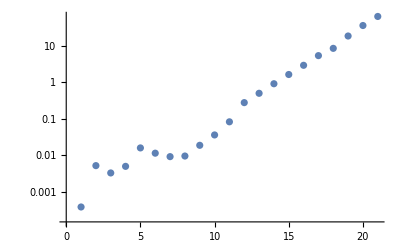

```mathematica
ListLogPlot[times]
```

### Junk

```mathematica
(*SnChar[n_,NN_]:=Module[{},
script="LoadPackage( \"ctbllib\" );;
	SnChar := function(n, N)
	\tlocal ct, irr, cp, short, part, sq, ans;
	\tct := CharacterTable(\"Symmetric\", n);;
	\tirr := Irr(ct);;
	\tcp := ClassParameters(ct);;
	\tshort := Filtered([1..Length(cp)], x->Length(cp[x][2]) <= N);;
	\tpart := List(cp, x -> x[2]);;
	\tsq := Sum(short, x -> irr[x] * irr[x]);;
	\tans := List([1..Length(part)], x -> [part[x], sq[x]]);;
	\tPrintTo(\"/Users/yinhslin/Downloads/index/output.txt\", ans);;
	end;;";
	script=script<>"
	SnChar("<>ToString[n]<>","<>ToString[NN]<>");;";

Export[NotebookDirectory[]<>"sym.txt",script];
DeleteFile[NotebookDirectory[]<>"sym.g"];
RenameFile[NotebookDirectory[]<>"sym.txt",NotebookDirectory[]<>"sym.g"];
gap="/Users/yinhslin/Downloads/gap-4.12.2/gap";
Run[gap<>" -q < "<>NotebookDirectory[]<>"sym.g"];

output=Import[NotebookDirectory[]<>"output.txt"];
output=StringReplace[output,{"["->"{","]"->"}"}]//ToExpression;
output
];*)
```

## GroupMath

```mathematica
<<GroupMath`
```

paclet:GroupMath/tutorial/GroupMathDoc | XXXXXXXXXXXXXXXXXXXXXXXXXXX GroupMath XXXXXXXXXXXXXXXXXXXXXXXXXXVersion: 1.1.2 (6/May/2020)Author: Renato FonsecaReference: 2011.01764 [hep-th]Website: http://renatofonseca.net/groupmathBuilt-in documentation: paclet:GroupMath/tutorial/GroupMathDocXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXX

SetDelayed::write: Tag BlockDiagonalMatrix in BlockDiagonalMatrix[blocks_] is Protected.

### Sn characters complexity analysis

```mathematica
partitions=IntegerPartitions[30];
shortPartitions=Select[partitions,Length[#]<=5&];
```

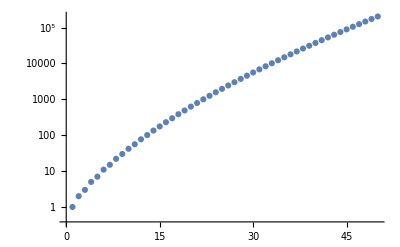

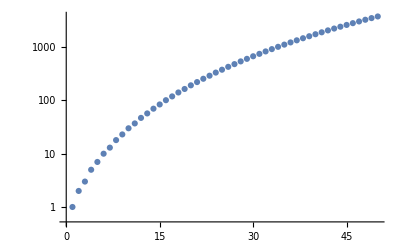

```mathematica
ListLogPlot[Table[Length[IntegerPartitions[n]],{n,1,50}]]
ListLogPlot[Table[Length[Select[IntegerPartitions[n],Length[#]<=5&]],{n,1,50}]]
```

### 1/16 unrefined index

```mathematica
z[P_]:=(Times@@P)Product[i[[2]]!,{i,Tally[P]}]
is[x_]:=1-((1-x^2)^3)/((1-x^3)^2)
index[N_,level_]:=Module[{partitions,shortPartitions},
partitions=IntegerPartitions[level];
shortPartitions=Select[partitions,Length[#]<=N&];
Sum[
Product[is[x^i],{i,P}] 1/z[P]
SnClassCharacter[λ,P]^2
,{λ,shortPartitions},{P,partitions}]
]
```

```mathematica
n=18;
Series[Sum[index[2,i],{i,1,n}],{x,0,2n+1}]
```

3 x^2-2 x^3+9 x^4-6 x^5+11 x^6-6 x^7+9 x^8+14 x^9-21 x^10+36 x^11-17 x^12-18 x^13+114 x^14-194 x^15+258 x^16-168 x^17-112 x^18+630 x^19-1089 x^20+1130 x^21-273 x^22-1632 x^23+4104 x^24-5364 x^25+3426 x^26+3152 x^27-13233 x^28+21336 x^29-18319 x^30-2994 x^31+40752 x^32-76884 x^33+78012 x^34-11808 x^35-121384 x^36+262206 x^37+O[x]^38

```mathematica
n=18;
Series[Sum[index[3,i],{i,1,n}],{x,0,2n+1}]
```

3 x^2-2 x^3+9 x^4-6 x^5+21 x^6-18 x^7+33 x^8-22 x^9+36 x^10+6 x^11-19 x^12+90 x^13-99 x^14+138 x^15-9 x^16-210 x^17+672 x^18-1116 x^19+1554 x^20-1270 x^21-36 x^22+2898 x^23-6705 x^24+10224 x^25-9918 x^26+2018 x^27+16470 x^28-42918 x^29+66906 x^30-66006 x^31+13566 x^32+106404 x^33-273204 x^34+407442 x^35-364710 x^36-12024 x^37+O[x]^38

### unflavored Schur index

```mathematica
z[P_]:=(Times@@P)Product[i[[2]]!,{i,Tally[P]}]
is[x_]:=1-(1-x)^2/(1-x^2)
index[N_,level_]:=Module[{partitions,shortPartitions},
partitions=IntegerPartitions[level];
shortPartitions=Select[partitions,Length[#]<=N&];
Sum[
Product[is[x^i],{i,P}] 1/z[P]
SnClassCharacter[λ,P]^2
,{λ,shortPartitions},{P,partitions}]
]
```

```mathematica
n=16;
Series[(1+Sum[index[2,i],{i,1,n}])/(1+Sum[index[1,i],{i,1,n}]),{x,0,n}]
```

1+3 x^2-4 x^3+9 x^4-12 x^5+22 x^6-36 x^7+60 x^8-88 x^9+135 x^10-204 x^11+302 x^12-432 x^13+627 x^14-900 x^15+1269 x^16+O[x]^17

```mathematica
n=10;
Series[(1+Sum[index[7,i],{i,1,n}])/(1+Sum[index[1,i],{i,1,n}]),{x,0,n}]
```

1+3 x^2+9 x^4+22 x^6+42 x^8+81 x^10+O[x]^11

## Mathematica built in FiniteGroupData

```mathematica
z[P_]:=(Times@@P)Product[i[[2]]!,{i,Tally[P]}]
is[x_]:=1-((1-x^2)^3)/((1-x^3)^2)
index[N_,level_]:=Module[{partitions,shortPartitions},
partitions=IntegerPartitions[level];
shortPartitions=Select[partitions,Length[#]<=N&];
Sum[
Product[is[x^i],{i,partitions[[k]]}] 1/z[partitions[[k]]]
FiniteGroupData[{"SymmetricGroup",level},"CharacterTable"][[j,Length[partitions]-k+1]]^2
,{j,1,Length[shortPartitions]},{k,1,Length[partitions]}]
]
```

```mathematica
Series[Sum[index[2,i],{i,1,10}],{x,0,12}]
```

3 x^2-2 x^3+9 x^4-6 x^5+11 x^6-6 x^7+9 x^8+14 x^9-21 x^10+36 x^11+81 x^12+O[x]^13

```mathematica
FiniteGroupData[{"SymmetricGroup",11},"CharacterTable"]
```

Missing[NotAvailable]

## Direct input

```mathematica
index[N_,level_]:=Module[{partitions,shortPartitions},
partitions=IntegerPartitions[level];
shortPartitions=Select[partitions,Length[#]<=N&];
Sum[
Product[is[x^i],{i,partitions[[k]]}] 1/z[partitions[[k]]]
χ[shortPartitions[[j]],partitions[[k]]]^2
,{j,1,Length[shortPartitions]},{k,1,Length[partitions]}]
]
 χ[{1},{1}]=1;
 χ[{1,1},{1,1}]=1;
 χ[{1,1},{2}]=-1;
 χ[{2},{1,1}]=1;
χ[{2},{2}]=1;
χ[{1,1,1},{1,1,1}]=1;
χ[{1,1,1},{2,1}]=-1;
χ[{1,1,1},{3}]=1;
χ[{2,1},{1,1,1}]=2;
χ[{2,1},{2,1}]=0;
χ[{2,1},{3}]=-1;
χ[{3},{1,1,1}]=1;
χ[{3},{2,1}]=1;
χ[{3},{3}]=1;
```